对称分量法

1、三相相电压

```mathematica
Uxxx=220;
Ua=220;
Ub=220;
Uc=195;
f=50;
w=2 Pi f;
uAN=Sqrt[2]*Ua*Cos[wt];
uBN=Sqrt[2]*Ub*Cos[wt-2*Pi/3];
uCN=Sqrt[2]*Uc*Cos[wt+2*Pi/3];
uN=uAN+uBN+uCN
```

220 √2 Cos[wt]-220 √2 Sin[π/6-wt]-195 √2 Sin[π/6+wt]

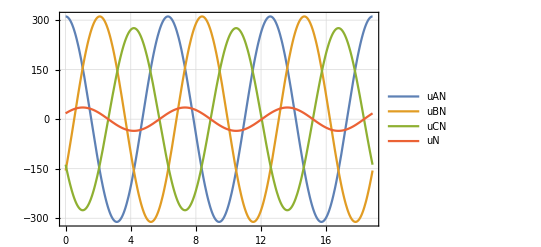

```mathematica
Plot[{uAN,uBN,uCN,uN},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

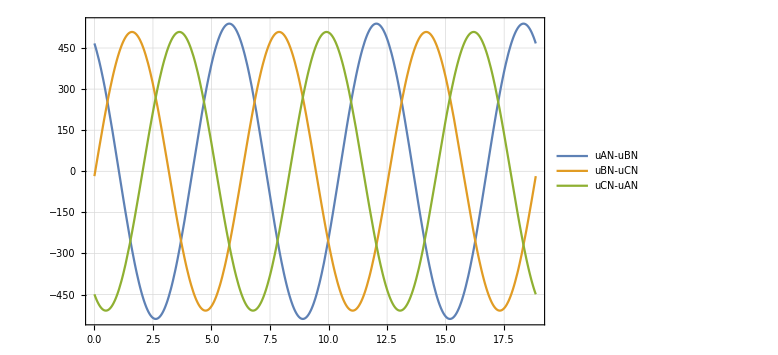

```mathematica
Plot[{uAN-uBN,uBN-uCN,uCN-uAN},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions",ImageSize->Large]
```

2、三相电压的相量表示

旋转算子

```mathematica
rot=E^(I 2 Pi/3)
```

ⅇ^((2 ⅈ π)/3)

三相相电压的相量

```mathematica
UAN=Ua;
UBN=Ub rot^2;
UCN=Uc rot;
```

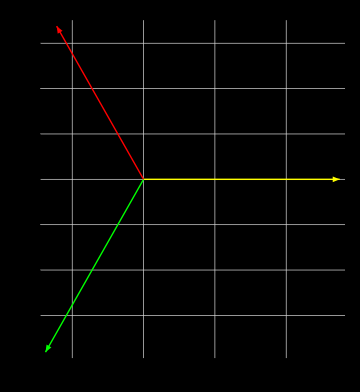

```mathematica
Graphics[{
Thick,Yellow,Arrow[{{0,0},{Re[UAN],Im[UAN]}}],
Thick,Green,Arrow[{{0,0},{Re[UBN],Im[UBN]}}],
Thick,Red,Arrow[{{0,0},{Re[UCN],Im[UCN]}}]},
Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium]
```

三相电压波形

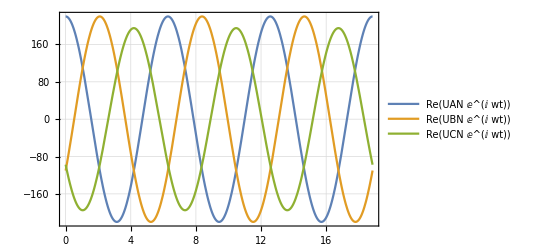

```mathematica
Plot[{Re[UAN*E^(I wt)],Re[UBN*E^(I wt)],Re[UCN*E^(I wt)]},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

3、正序分量、负序分量和零序分量

三相电压可以分解成正序分量、负序分量和零序分量
        -Graphics-
               -Graphics-
正序分量

```mathematica
UANP=(UAN+UBN*rot+UCN*rot^2)/3;
UBNP=UANP*rot^2;
UCNP=UANP*rot;
```

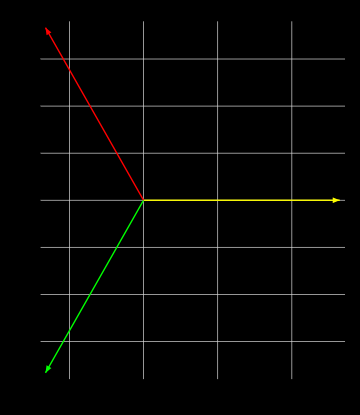

```mathematica
Graphics[{Thick,Yellow,Arrow[{{0,0},{Re[UANP],Im[UANP]}}],Thick,Green,Arrow[{{0,0},{Re[UBNP],Im[UBNP]}}],Thick,Red,Arrow[{{0,0},{Re[UCNP],Im[UCNP]}}]},Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium]
```

三相电压正序波形

```mathematica
uANP=ExpToTrig[UANP*E^(I wt)]
uBNP=ExpToTrig[UBNP*E^(I wt)]
uCNP=ExpToTrig[UCNP*E^(I wt)]
```

(635 Cos[wt])/3+635/3 ⅈ Sin[wt]

-635/3 ⅈ Cos[π/6-wt]-635/3 Sin[π/6-wt]

635/3 ⅈ Cos[π/6+wt]-635/3 Sin[π/6+wt]

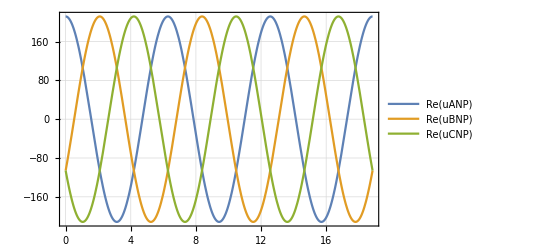

```mathematica
Plot[{Re[uANP],Re[uBNP],Re[uCNP]},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

负序分量

```mathematica
UANN=(UAN+UBN*rot^2+UCN*rot)/3;
UBNN=UANN*rot;
UCNN=UANN*rot^2;
```

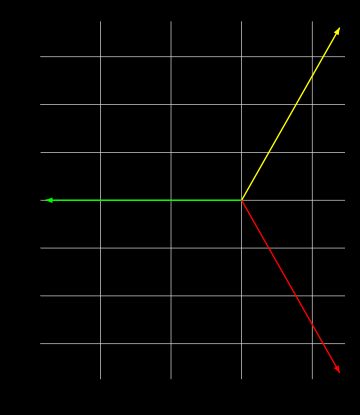

```mathematica
Graphics[{Thick,Yellow,Arrow[{{0,0},{Re[UANN],Im[UANN]}}],Thick,Green,Arrow[{{0,0},{Re[UBNN],Im[UBNN]}}],Thick,Red,Arrow[{{0,0},{Re[UCNN],Im[UCNN]}}]},Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium]
```

三相电压负序波形

```mathematica
uANN=UANN*E^(I wt)
uBNN=UBNN*E^(I wt)
uCNN=UCNN*E^(I wt)
```

1/3 ⅇ^(ⅈ wt) (220+195 ⅇ^(-(2 ⅈ π)/3)+220 ⅇ^((2 ⅈ π)/3))

1/3 ⅇ^((2 ⅈ π)/3+ⅈ wt) (220+195 ⅇ^(-(2 ⅈ π)/3)+220 ⅇ^((2 ⅈ π)/3))

1/3 ⅇ^(-(2 ⅈ π)/3+ⅈ wt) (220+195 ⅇ^(-(2 ⅈ π)/3)+220 ⅇ^((2 ⅈ π)/3))

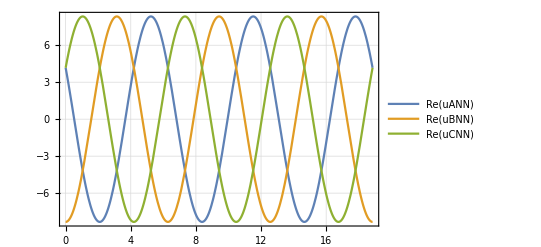

```mathematica
Plot[{Re[uANN],Re[uBNN],Re[uCNN]},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

零序分量

```mathematica
UANZ=(UAN+UBN+UCN)/3;
UBNZ=UANZ;
UCNZ=UANZ;
```

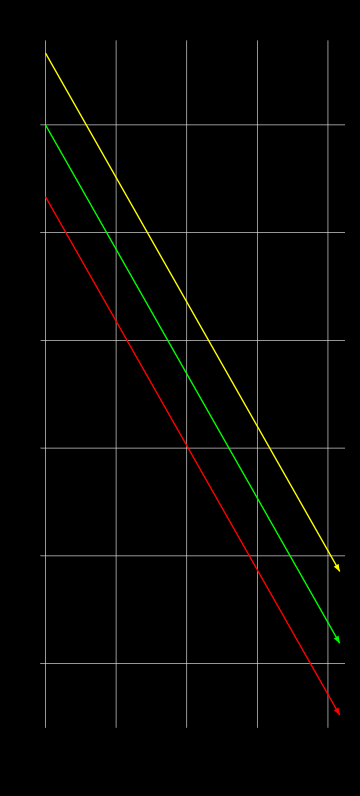

```mathematica
Graphics[{Thick,Yellow,Arrow[{{0,0+1},{Re[UANZ],Im[UANZ]+1}}],Thick,Green,Arrow[{{0,0},{Re[UBNZ],Im[UBNZ]}}],Thick,Red,Arrow[{{0,0-1},{Re[UCNZ],Im[UCNZ]-1}}]},Frame->True,GridLines->Automatic,Background->Black,ImageSize->Medium]
```

三相电压零序波形

```mathematica
uANZ=UANZ*E^(I wt)
uBNZ=UBNZ*E^(I wt)
uCNZ=UCNZ*E^(I wt)
```

1/3 ⅇ^(ⅈ wt) (220+220 ⅇ^(-(2 ⅈ π)/3)+195 ⅇ^((2 ⅈ π)/3))

1/3 ⅇ^(ⅈ wt) (220+220 ⅇ^(-(2 ⅈ π)/3)+195 ⅇ^((2 ⅈ π)/3))

1/3 ⅇ^(ⅈ wt) (220+220 ⅇ^(-(2 ⅈ π)/3)+195 ⅇ^((2 ⅈ π)/3))

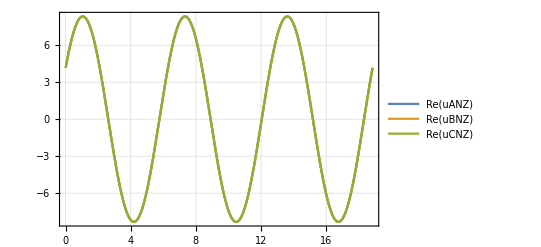

```mathematica
Plot[{Re[uANZ],Re[uBNZ],Re[uCNZ]},{wt,0,6*Pi},Frame->True,GridLines->Automatic,PlotLegends->"Expressions"]
```

## 4、不平衡度

根据国标GB/T 15543-2008。
不平衡度指三相电力系统中三相不平衡的程度。用电压、电流负序基波分量或零序基波分量与正序基波分量的方均根值百分比表示。电压、电流的负序不平衡度和零序不平衡度分别用ϵ_U2、ϵ_U0和ϵ_I2、ϵ_I0表示。
-Graphics-
-Graphics-
-Graphics-
根据A.1公式，可计算出负序分量的不平衡度如下

```mathematica
Subscript[ϵ, U2]=Norm[UANN]/Norm[UANP] //N
```

0.0393701